## Analysis of the error and model convergence

We want to study the model error for each reduced system and make an overall comparison of the errors.
Therefore, for each system, the same experiment is repeated in different regimes of shallowness.
For each outcome, the deviation of the model result from the reference result is determined.
The plots show the error depending on the degree of shallowness.

## Preliminaries

```mathematica
(* clear the scope *)
contexts=(#<>"*")&/@{"Global`","FreeSurf`","DSM0`","DSM1`","DSM2`","DSM3`","GN`"};
Quiet[Remove/@ contexts];
```

```mathematica
(* set directory of the engine folder *)
engineDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"engine"}];
```

```mathematica
(* load engines *)
Get[FileNameJoin[{engineDirectory,"FreeSurf.wl"}]] 
Get[FileNameJoin[{engineDirectory,"DSM0.wl"}]] 
Get[FileNameJoin[{engineDirectory,"DSM1.wl"}]] 
Get[FileNameJoin[{engineDirectory,"DSM2.wl"}]] 
Get[FileNameJoin[{engineDirectory,"DSM3.wl"}]] 
Get[FileNameJoin[{engineDirectory,"GN.wl"}]]
```

```mathematica
(* some option for nicer plots *)
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"];
```

## Set parameters and error function

```mathematica
(* set parameters *)
Fr=.6;n=90;η=.09; σ=.25;
(* the different degrees of shallowness to be taken into account *)
hSteps=Table[H,{H,.05,.5,.05}];
```

```mathematica
(* define error functions.*)
errL1[testData_,referenceData_, var_]:=N@Integrate[Abs[(var[x] /. testData) - (var[x] /. referenceData)],{x,-1,1}];
errL1[var_]:=errL1[#1,#2,var]&;
errInf[testData_,referenceData_,var_]:=NMaximize[{Abs[(var[x]/.testData)-(var[x]/.referenceData)],x≥-1,x≤1},x]⟦1⟧
errInf[var_]:=errInf[#1,#2,var]&;
```

```mathematica
(* We will use the infinity error*)
err=errInf;
```

## Calculate data

```mathematica
freeSurfData=FreeSurf[#,Fr,# η,σ,n]&/@hSteps;
```

```mathematica
dsm0Data=DSM0[#,Fr,# η,σ,n]&/@hSteps;
dsm1Data=DSM1[#,Fr,# η,σ,n]&/@hSteps;
dsm2Data=DSM2[#,Fr,# η,σ,n]&/@hSteps;
dsm3Data=DSM3[#,Fr,# η,σ,n]&/@hSteps;
gnData=GN[#,Fr,# η,σ,n]&/@hSteps;
```

## Calculate errors

```mathematica
dsm0hErrors=MapThread[err[h],{dsm0Data,freeSurfData}];
dsm1hErrors=MapThread[err[h],{dsm1Data,freeSurfData}];
dsm2hErrors=MapThread[err[h],{dsm2Data,freeSurfData}];
dsm3hErrors=MapThread[err[h],{dsm3Data,freeSurfData}];
gnhErrors=MapThread[err[h],{gnData,freeSurfData}];
```

```mathematica
dsm0umErrors=MapThread[err[um],{dsm0Data,freeSurfData}];
dsm1umErrors=MapThread[err[um],{dsm1Data,freeSurfData}];
dsm2umErrors=MapThread[err[um],{dsm2Data,freeSurfData}];
dsm3umErrors=MapThread[err[um],{dsm3Data,freeSurfData}];
gnumErrors=MapThread[err[um],{gnData,freeSurfData}];
```

```mathematica
dsm0wmErrors=MapThread[err[wm],{dsm0Data,freeSurfData}];
dsm1wmErrors=MapThread[err[wm],{dsm1Data,freeSurfData}];
dsm2wmErrors=MapThread[err[wm],{dsm2Data,freeSurfData}];
dsm3wmErrors=MapThread[err[wm],{dsm3Data,freeSurfData}];
gnwmErrors=MapThread[err[wm],{gnData,freeSurfData}];
```

```mathematica
dsm0qmErrors=MapThread[err[qm],{dsm0Data,freeSurfData}];
dsm1qmErrors=MapThread[err[qm],{dsm1Data,freeSurfData}];
dsm2qmErrors=MapThread[err[qm],{dsm2Data,freeSurfData}];
dsm3qmErrors=MapThread[err[qm],{dsm3Data,freeSurfData}];
gnqmErrors=MapThread[err[qm],{gnData,freeSurfData}];
```

## Create plots

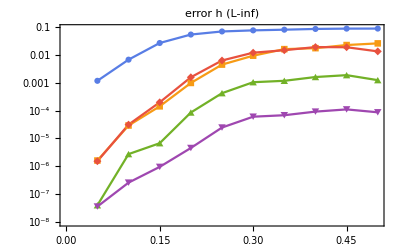

```mathematica
pConvergenceh=ListLogPlot[
TemporalData[{dsm0hErrors,gnhErrors,dsm1hErrors,dsm2hErrors,dsm3hErrors},{hSteps}],PlotMarkers->Automatic,
Frame->True,
PlotRange->
{{Full,Full},{10^-8,Full}},
GridLines->Automatic,
GridLinesStyle->Directive[Black,Opacity[1],Thickness[.005]],
FrameStyle->Directive[Black,Opacity[1],Thickness[.005]],
LabelStyle->Directive[14,Black],
Joined->True,
ImagePadding->{{50,45},{35,25}},
PlotTheme->"BoldColor", PlotLabel->"error h (L-inf)",
PlotRange->{{.03,.4},{0,2}}
]
```

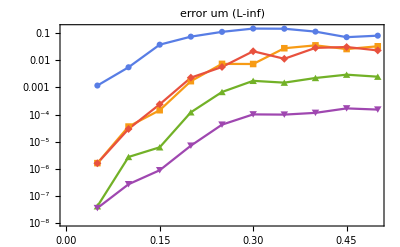

```mathematica
pConvergenceum=ListLogPlot[
TemporalData[{dsm0umErrors,gnumErrors,dsm1umErrors,dsm2umErrors,dsm3umErrors},{hSteps}],
PlotMarkers->Automatic,
Frame->True,
PlotRange->Full,
GridLines->Automatic,
GridLinesStyle->Directive[Black,Opacity[1],Thickness[.005]],
FrameStyle->Directive[Black,Opacity[1],Thickness[.005]],
LabelStyle->Directive[14,Black],
Joined->True,
ImagePadding->{{50,45},{35,25}},
PlotTheme->"BoldColor",PlotLabel->"error um (L-inf)"
]
```

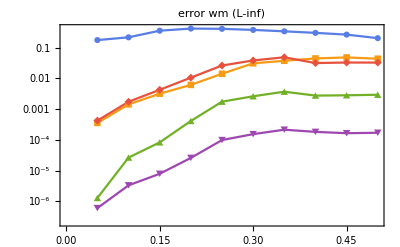

```mathematica
pConvergencewm=ListLogPlot[
TemporalData[{dsm0wmErrors,gnwmErrors,dsm1wmErrors,dsm2wmErrors,dsm3wmErrors},{hSteps}],
PlotMarkers->Automatic,
Frame->True,
PlotRange->Full,
GridLines->Automatic,
GridLinesStyle->Directive[Black,Opacity[1],Thickness[.005]],
FrameStyle->Directive[Black,Opacity[1],Thickness[.005]],
LabelStyle->Directive[14,Black],
Joined->True,
ImagePadding->{{50,45},{35,25}},
PlotTheme->"BoldColor",PlotLabel->"error wm (L-inf)"
]
```

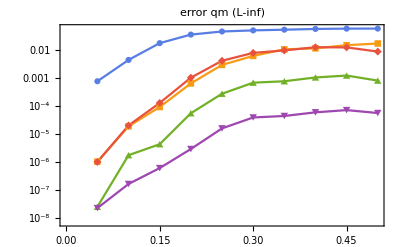

```mathematica
pConvergenceqm=ListLogPlot[
TemporalData[{dsm0qmErrors,gnqmErrors,dsm1qmErrors,dsm2qmErrors,dsm3qmErrors},{hSteps}],
PlotMarkers->Automatic,
Frame->True,
PlotRange->Full,
GridLines->Automatic,
GridLinesStyle->Directive[Black,Opacity[1],Thickness[.005]],
FrameStyle->Directive[Black,Opacity[1],Thickness[.005]],
LabelStyle->Directive[14,Black],
Joined->True,
ImagePadding->{{50,45},{35,25}},
PlotTheme->"BoldColor",PlotLabel->"error qm (L-inf)"
]
```